```mathematica
PS[n_] := PS[n]= FullSimplify[MangoldtLambda[ n]/Log[n]]
DD[n_, k_, a_] :=  DD[n,k,a] = Sum[ PS[j](a^k/k! + DD[n/j, k+1,a]), {j,2,n}]
Dd[ n_, a_ ]:= Dd[n,a] = DD[n,1,a]-DD[n-1,1,a]
D2[n_,k_] := Sum[ D2[n/j, k-1], {j,2,n}]
D2[n_,0] := 1
Dd2[ n_, k_] := D2[n,k] - D2[n-1,k]
```

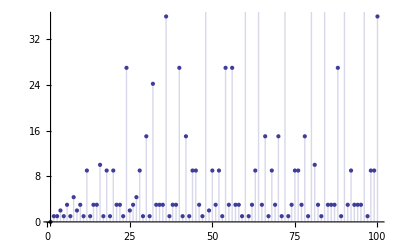

```mathematica
DiscretePlot[PPS[n,-2]-PPS[n-1,-2],{n,100}]
```

```mathematica
PSA[n_, a_ ] := PPS[n,a]-PPS[n-1,a]
```

```mathematica
PSA[30,1]
```

0

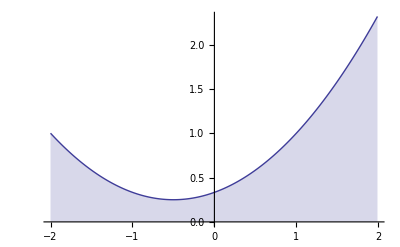

```mathematica
DiscretePlot[PSA[8,-j+1] ,{j,-2 + .0000001,2, .01}]
```

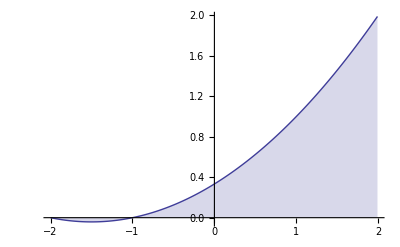

```mathematica
DiscretePlot[Dd[8,j]/j ,{j,-2 + .0000001,2, .01}]
```

```mathematica
PPR[n_, k_, a_] := PPR[n,k,a] = Sum[a ( 1/k - PPR[n/j, k+1,a]), { j, 2, n }]
PPS[n_, a_] := PPR[n,1,a]/a
```

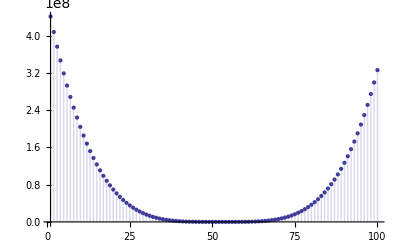

```mathematica
DiscretePlot[Re[PPS[46,1+I(-221.001 + 422 *(n/100))]] ,{n,100}]
```